```mathematica
genxList[n_:4] := π/4 Cos[(π(2*#+1))/(2(n+1))]+π/4&/@Range[0,n];
xList2={π/12,(5π)/12,(7π)/24};
func[x_]:=Sin[x];
n=4;
```

```mathematica
xList = N@genxList[n]
```

{1.53236,1.24704,0.785398,0.323753,0.0384401}

```mathematica
L[func_,x_,deg_,fst_:0]:=Return[Expand@N@(1/(xList[[fst+deg+1]]-xList[[fst+1]]))*If[deg==1,
Det[{func[xList[[fst+1;;fst+1+deg]]],xList[[{fst+1,fst+1+deg}]]-x}],
Det[{{L[func,x,deg-1,fst],L[func,x,deg-1,fst+1]},xList[[{fst+1,fst+1+deg}]]-x}]]]
```

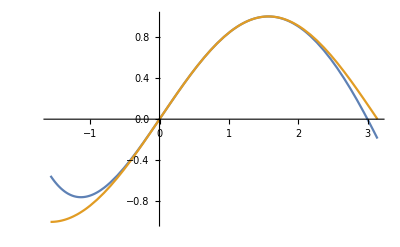

```mathematica
Plot[{Expand@L[func,x,n],func[x]},{x,-π/2,π}]
```

### общий вид таблицы

```mathematica
matr1=Transpose[{"x"<>ToString@#&/@Range[0,Length[xList]-1],
"y"<>ToString@#&/@Range[0,Length[xList]-1],
"x"<>ToString@#<>"-x"&/@Range[0,Length[xList]-1],
Sequence@@Array[""&,{Length[xList]-1,Length[xList]}]
}];
```

```mathematica
matr2=Transpose[{xList,
N@func@xList,
xList-x,
Sequence@@Array[""&,{Length[xList]-1,Length[xList]}]
}]
```

{{1.53236,0.999261,1.53236-x,,,,},{1.24704,0.948048,1.24704-x,,,,},{0.785398,0.707107,0.785398-x,,,,},{0.323753,0.318127,0.323753-x,,,,},{0.0384401,0.0384307,0.0384401-x,,,,}}

```mathematica
Table[Set[matr1[[fst+deg+1,deg+3]],Expand@N@L[func,x,deg,fst]],{deg,1,Length[xList]-1},{fst,0,Length[xList]-1-deg}];
Table[Set[matr2[[fst+deg+1,deg+3]],Expand@N@L[func,x,deg,fst]],{deg,1,Length[xList]-1},{fst,0,Length[xList]-1-deg}];
```

```mathematica
gridMatr1=Grid[matr1,Frame->All];
gridMatr2=Grid[matr2,Frame->All];
```

```mathematica
gridMatr1
gridMatr2
```

x0 | y0 | x0-x |  |  |  | 
x1 | y1 | x1-x | 0.724207+0.179498 x |  |  | 
x2 | y2 | x2-x | 0.297193+0.521919 x | -0.151796+1.45363 x-0.458421 x^2 |  | 
x3 | y3 | x3-x | 0.0453341+0.842595 x | -0.0429804+1.22782 x-0.347319 x^2 | -0.0138314+1.0773 x-0.130724 x^2-0.0919258 x^3 | 
x4 | y4 | x4-x | 0.000747271+0.980314 x | -0.00154726+1.04709 x-0.184373 x^2 | -0.000229468+1.00706 x-0.0296524 x^2-0.134822 x^3 | 0.000120526+0.99615 x+0.0199653 x^2-0.203581 x^3+0.0287138 x^4

1.53236 | 0.999261 | 1.53236-x |  |  |  | 
1.24704 | 0.948048 | 1.24704-x | 0.724207+0.179498 x |  |  | 
0.785398 | 0.707107 | 0.785398-x | 0.297193+0.521919 x | -0.151796+1.45363 x-0.458421 x^2 |  | 
0.323753 | 0.318127 | 0.323753-x | 0.0453341+0.842595 x | -0.0429804+1.22782 x-0.347319 x^2 | -0.0138314+1.0773 x-0.130724 x^2-0.0919258 x^3 | 
0.0384401 | 0.0384307 | 0.0384401-x | 0.000747271+0.980314 x | -0.00154726+1.04709 x-0.184373 x^2 | -0.000229468+1.00706 x-0.0296524 x^2-0.134822 x^3 | 0.000120526+0.99615 x+0.0199653 x^2-0.203581 x^3+0.0287138 x^4

### π/12

```mathematica
N@Grid[matr2/.x->xList2[[1]],Frame->All]
```

1.53236 | 0.999261 | 1.27056 |  |  |  | 
1.24704 | 0.948048 | 0.985244 | 0.771199 |  |  | 
0.785398 | 0.707107 | 0.523599 | 0.433831 | 0.197344 |  | 
0.323753 | 0.318127 | 0.0619533 | 0.265925 | 0.254658 | 0.257596 | 
0.0384401 | 0.0384307 | -0.223359 | 0.257393 | 0.259944 | 0.258967 | 0.258762

### (5π)/12

```mathematica
N@Grid[matr2/.x->xList2[[2]],Frame->All]
```

1.53236 | 0.999261 | 0.223359 |  |  |  | 
1.24704 | 0.948048 | -0.0619533 | 0.959169 |  |  | 
0.785398 | 0.707107 | -0.523599 | 0.980383 | 0.965512 |  | 
0.323753 | 0.318127 | -0.985244 | 1.14829 | 0.969116 | 0.966178 | 
0.0384401 | 0.0384307 | -1.27056 | 1.28398 | 1.05318 | 0.964807 | 0.965973

### (7π)/24

```mathematica
N@Grid[matr2/.x->xList2[[3]],Frame->All]
```

1.53236 | 0.999261 | 0.616058 |  |  |  | 
1.24704 | 0.948048 | 0.330746 | 0.88868 |  |  | 
0.785398 | 0.707107 | -0.1309 | 0.775426 | 0.795273 |  | 
0.323753 | 0.318127 | -0.592545 | 0.817402 | 0.790463 | 0.792821 | 
0.0384401 | 0.0384307 | -0.877858 | 0.899007 | 0.803102 | 0.793922 | 0.793275

### погрешности

```mathematica
xList = π*{0,1/6,1/4,1/3,1/2};
a1 = L[func,#,n]&/@xList2;
xList = genxList[];
a2 = L[func,#,n]&/@xList2;
b = N@func[xList2];
```

```mathematica
"по 'просто' узлам"
Abs[a1-b]
"по оптимальным узлам"
Abs[a2-b]
```

по 'просто' узлам

{0.000231136,0.000193837,0.000022872}

по оптимальным узлам

{0.0000567062,0.0000475509,0.0000784734}

```mathematica
maxf = FindMaximum[Abs[D[func[x],{x,n+1}]],{x,0,π/2}][[1]];
b=π/2;
a=0;
2*((b-a)/4)^(n+1)*maxf/Factorial[n+1]
```

0.00015565